```mathematica
(*********************************************************)
(*                                                         *)
(*   Constructing Hamiltonian                              *)
(*                                                         *)
(*********************************************************)
```

```mathematica
Unit[H_]:=FullSimplify[MatrixExp[-ⅈ*H]]
```

```mathematica
S = {{1,0,0,0},
    {0,0,1,0},
    {0,1,0,0},
    {0,0,0,1}};
eye = {{1,0},{0,1}};
eye2=KroneckerProduct[eye,eye];
```

```mathematica
U = KroneckerProduct[S,eye].KroneckerProduct[eye,S];
U//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
H = FullSimplify[MatrixLog[U]*ⅈ];
H/((2 ⅈ π)/(3 √3))//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Unit[H]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
U2 = S;
U2.U2//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
H2 = FullSimplify[MatrixLog[U2]*ⅈ];
H2*2/Pi//MatrixForm
```

(0 | 0 | 0 | 0
0 | -1 | 1 | 0
0 | 1 | -1 | 0
0 | 0 | 0 | 0)

```mathematica
Unit[H2]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
U4 = KroneckerProduct[S,eye, eye].KroneckerProduct[eye,S,eye].KroneckerProduct[eye,eye,S];
U4//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
H4= FullSimplify[MatrixLog[U4]*ⅈ];
H4*4/Pi//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1+ⅈ | 0 | -1 | 0 | 0 | 0 | 1-ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1-ⅈ | -1 | 0 | 1+ⅈ | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 1+ⅈ | 0 | 0 | 1-ⅈ | 0 | 0 | -1 | 0 | 0 | 0
0 | -1 | 1-ⅈ | 0 | -1 | 0 | 0 | 0 | 1+ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1-ⅈ | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1+ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1-ⅈ | 0 | -1 | 1+ⅈ | 0
0 | 1+ⅈ | -1 | 0 | 1-ⅈ | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1+ⅈ | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1-ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1+ⅈ | 0 | 0 | 0 | -1 | 0 | 1-ⅈ | -1 | 0
0 | 0 | 0 | -1 | 0 | 0 | 1-ⅈ | 0 | 0 | 1+ⅈ | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1+ⅈ | 0 | -1 | 1-ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1-ⅈ | 0 | 0 | 0 | -1 | 0 | 1+ⅈ | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvalues[H4]
```

{-π,-π,-π,-π,-π/2,-π/2,-π/2,π/2,π/2,π/2,0,0,0,0,0,0}

```mathematica
Unit[H4]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
vec = Eigenvectors[H];
Eigenvalues[H]
val = DiagonalMatrix[Eigenvalues[H]];
ConjugateTranspose[vec]//MatrixForm
```

{-(2 π)/3,-(2 π)/3,(2 π)/3,(2 π)/3,0,0,0,0}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1/2 (-1-ⅈ √3) | 0 | 1/2 (-1+ⅈ √3) | 0 | 0 | 1 | 0
0 | 1/2 (-1+ⅈ √3) | 0 | 1/2 (-1-ⅈ √3) | 0 | 0 | 1 | 0
1/2 (-1+ⅈ √3) | 0 | 1/2 (-1-ⅈ √3) | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1/2 (-1-ⅈ √3) | 0 | 1/2 (-1+ⅈ √3) | 0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
FullSimplify[ConjugateTranspose[vec].val.vec]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(2 ⅈ π)/(√3) | 0 | (2 ⅈ π)/(√3) | 0 | 0 | 0
0 | (2 ⅈ π)/(√3) | 0 | 0 | -(2 ⅈ π)/(√3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 ⅈ π)/(√3) | -(2 ⅈ π)/(√3) | 0
0 | -(2 ⅈ π)/(√3) | (2 ⅈ π)/(√3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(2 ⅈ π)/(√3) | 0 | 0 | (2 ⅈ π)/(√3) | 0
0 | 0 | 0 | (2 ⅈ π)/(√3) | 0 | -(2 ⅈ π)/(√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
plus = 1/2 (-1-ⅈ √3);
minus = 1/2 (-1+ⅈ √3);
Eplus = 2*Pi/3;
Eminus = -2*Pi/3;
```

```mathematica
cob = {{√3,0,0, 0,         0,         0,         0,         0},
             {0,1,0,0,  plus,         0,minus,         0},
             {0,1,0,0,minus,         0,plus,           0},
             {0,0,1,0,         0,         1,         0,         1},
             {0,1,0,0,         1,         0,         1,         0},
             {0,0,1,0,         0,minus,         0,  plus},
             {0,0,1,0,         0,  plus,         0,minus},
             {0,0,0,√3,     0,         0,         0,         0}}/√3;
ener = DiagonalMatrix[{0,0,0,0,Eplus,Eplus,Eminus,Eminus}];
(*ener = DiagonalMatrix[{0,0,0,0,0,0,0,Eminus}];*)
ener//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (2 π)/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 π)/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(2 π)/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 π)/3)

```mathematica
FullSimplify[cob  . ener. ConjugateTranspose[cob]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 ⅈ π)/(3 √3) | 0 | -(2 ⅈ π)/(3 √3) | 0 | 0 | 0
0 | -(2 ⅈ π)/(3 √3) | 0 | 0 | (2 ⅈ π)/(3 √3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(2 ⅈ π)/(3 √3) | (2 ⅈ π)/(3 √3) | 0
0 | (2 ⅈ π)/(3 √3) | -(2 ⅈ π)/(3 √3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (2 ⅈ π)/(3 √3) | 0 | 0 | -(2 ⅈ π)/(3 √3) | 0
0 | 0 | 0 | -(2 ⅈ π)/(3 √3) | 0 | (2 ⅈ π)/(3 √3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[Unit[cob  . ener. ConjugateTranspose[cob] t]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 (1+2 Cos[(2 π t)/3]) | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 0 | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 0 | 0 | 0
0 | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 1/3 (1+2 Cos[(2 π t)/3]) | 0 | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 0 | 0 | 0
0 | 0 | 0 | 1/3 (1+2 Cos[(2 π t)/3]) | 0 | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 0
0 | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 0 | 1/3 (1+2 Cos[(2 π t)/3]) | 0 | 0 | 0
0 | 0 | 0 | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 0 | 1/3 (1+2 Cos[(2 π t)/3]) | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 0
0 | 0 | 0 | 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]) | 0 | 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]) | 1/3 (1+2 Cos[(2 π t)/3]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Spin3 = DiagonalMatrix[{0,1,1,2,1,2,2,3}];
Spin3.H - H.Spin3 //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*********************************************************)
(*                                                         *)
(*   3 spin                                                *)
(*                                                         *)
(*********************************************************)
```

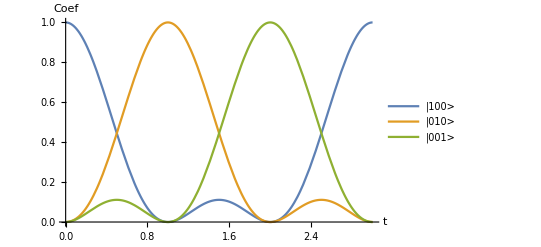

```mathematica
Plot[{
(1/3 (1+2 Cos[(2 π t)/3]))^2,
(1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]))^2,
(1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]))^2
},{t,0,3},BaseStyle->{FontSize->Scaled[.05]},PlotLegends->{"|100>","|010>","|001>"},AxesLabel->{t,"Coef"}]
```

```mathematica
(*********************************************************)
(*                                                         *)
(*   5 site sparse                                         *)
(*                                                         *)
(*********************************************************)
```

```mathematica
H5 = KroneckerProduct[H,eye2]+KroneckerProduct[eye2,H];
U5 = Unit[H5];
U5t = Unit[H5 t];
```

```mathematica
ConjugateTranspose[U5t][[2]]
```

{0,1/10 (2+3 Cos[2/3 √(5/3) π Conjugate[t]]+5 Cos[(2 π Conjugate[t])/(3 √3)]),1/10 (2-2 Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]-5 Sin[(2 π Conjugate[t])/(3 √3)]),0,1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]+√5 Sin[2/3 √(5/3) π Conjugate[t]]),0,0,0,1/10 (2+3 Cos[2/3 √(5/3) π Conjugate[t]]-5 Cos[(2 π Conjugate[t])/(3 √3)]),0,0,0,0,0,0,0,1/10 (2-2 Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]+5 Sin[(2 π Conjugate[t])/(3 √3)]),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

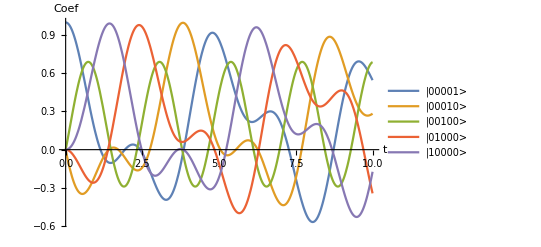

```mathematica
Plot[{
1/10 (2+3 Cos[2/3 √(5/3) π t]+5 Cos[(2 π t)/(3 √3)]),1/10 (2-2 Cos[2/3 √(5/3) π t]-√5 Sin[2/3 √(5/3) π t]-5 Sin[(2 π  t)/(3 √3)]),1/5 (1-Cos[2/3 √(5/3) π t]+√5 Sin[2/3 √(5/3) π t]),1/10 (2+3 Cos[2/3 √(5/3) π t]-5 Cos[(2 π t)/(3 √3)]),1/10 (2-2 Cos[2/3 √(5/3) π t]-√5 Sin[2/3 √(5/3) π t]+5 Sin[(2 π t)/(3 √3)])
},{t,0,10},BaseStyle->{FontSize->Scaled[.05]},PlotLegends->{"|00001>","|00010>","|00100>","|01000>","|10000>"},AxesLabel->{t,"Coef"}]
```

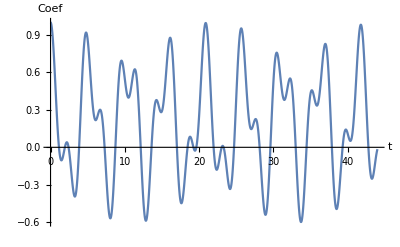

```mathematica
Plot[{1/10 (2+3 Cos[2/3 √(5/3) π t]+5 Cos[(2 π t)/(3 √3)])},{t,0,44},BaseStyle->{FontSize->Scaled[.05]},AxesLabel->{t,"Coef"}]
```

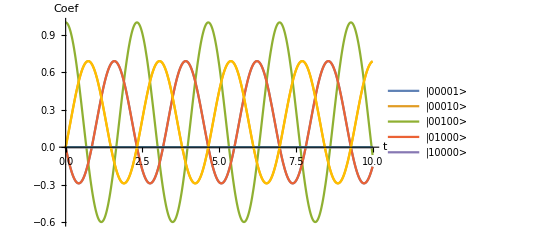

```mathematica
Plot[{
1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]),1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]+√5 Sin[2/3 √(5/3) π Conjugate[t]]),1/5 (1+4 Cos[2/3 √(5/3) π Conjugate[t]]),1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]),0,0,0,1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]+√5 Sin[2/3 √(5/3) π Conjugate[t]])},{t,0,10},PlotLegends->{"|00001>","|00010>","|00100>","|01000>","|10000>"},BaseStyle->{FontSize->Scaled[.05]},AxesLabel->{t,"Coef"}]
```

```mathematica
(*********************************************************)
(*                                                         *)
(*   5 site dense                                          *)
(*                                                         *)
(*********************************************************)
```

```mathematica
H5d = KroneckerProduct[H,eye2]+KroneckerProduct[eye2,H]+KroneckerProduct[KroneckerProduct[eye,H],eye];
```

```mathematica
{vals,vecs}=Eigensystem[N[H5d]];
```

```mathematica
U5dt=ConjugateTranspose[vecs].(Exp[-I Conjugate[t] vals]*vecs);
```

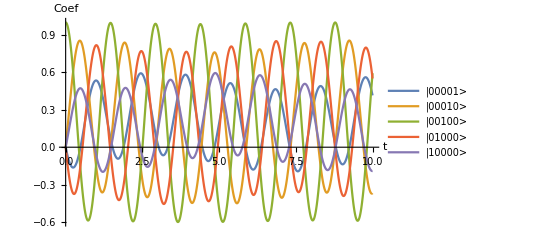

```mathematica
Plot[{
Re[Conjugate[U5dt][[5,2]]],
Re[Conjugate[U5dt][[5,3]]],
Re[Conjugate[U5dt][[5,5]]],
Re[Conjugate[U5dt][[5,9]]],
Re[Conjugate[U5dt][[5,17]]]
},{t,0,10},BaseStyle->{FontSize->Scaled[.05]},PlotLegends->{"|00001>","|00010>","|00100>","|01000>","|10000>"},AxesLabel->{t,"Coef"}]
```

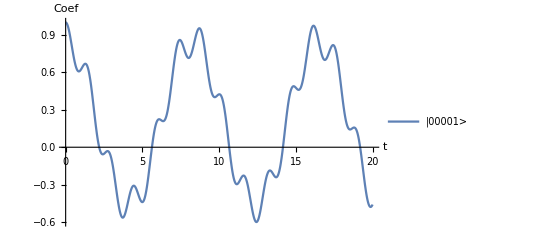

```mathematica
Plot[{
Re[Conjugate[U5dt][[2,2]]]
},{t,0,20},BaseStyle->{FontSize->Scaled[.05]},PlotLegends->{"|00001>","|00010>","|00100>","|01000>","|10000>"},AxesLabel->{t,"Coef"}]
```

```mathematica
Plot[{1/10 (2+3 Cos[2/3 √(5/3) π t]+5 Cos[(2 π t)/(3 √3)])},{t,0,44},BaseStyle->{FontSize->Scaled[.05]},AxesLabel->{t,"Coef"}]
```

-Graphics-

```mathematica
Plot[{
1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]),1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]+√5 Sin[2/3 √(5/3) π Conjugate[t]]),1/5 (1+4 Cos[2/3 √(5/3) π Conjugate[t]]),1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]-√5 Sin[2/3 √(5/3) π Conjugate[t]]),0,0,0,1/5 (1-Cos[2/3 √(5/3) π Conjugate[t]]+√5 Sin[2/3 √(5/3) π Conjugate[t]])},{t,0,10},PlotLegends->{"|00001>","|00010>","|00100>","|01000>","|10000>"},BaseStyle->{FontSize->Scaled[.05]},AxesLabel->{t,"Coef"}]
```

-Graphics-

```mathematica
(*********************************************************)
(*                                                         *)
(*   4 site                                                *)
(*                                                         *)
(*********************************************************)
```

```mathematica
H4 = KroneckerProduct[H,eye]+KroneckerProduct[eye,H];
```

```mathematica
U4 = Unit[H4];
U4t = Unit[H4 t];
```

```mathematica
ConjugateTranspose[U4t][[4]]
```

{0,0,0,1/4 (3+Cos[4/3 √(2/3) π Conjugate[t]]),0,1/2 Sin[2/3 √(2/3) π Conjugate[t]]^2,-Sin[4/3 √(2/3) π Conjugate[t]]/(2 √2),0,0,Sin[4/3 √(2/3) π Conjugate[t]]/(2 √2),-1/2 Sin[2/3 √(2/3) π Conjugate[t]]^2,0,1/2 Sin[2/3 √(2/3) π Conjugate[t]]^2,0,0,0}

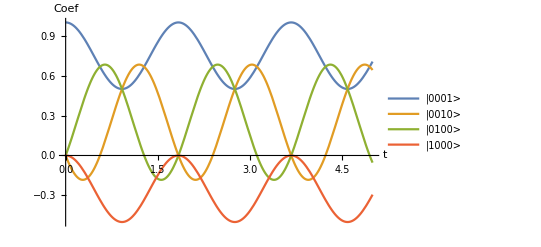

```mathematica
Plot[{
1/4 (3+Cos[4/3 √(2/3) π Conjugate[t]]),1/4 (1-Cos[4/3 √(2/3) π Conjugate[t]]-√2 Sin[4/3 √(2/3) π Conjugate[t]]),1/4 (1-Cos[4/3 √(2/3) π Conjugate[t]]+√2 Sin[4/3 √(2/3) π Conjugate[t]]),-1/2 Sin[2/3 √(2/3) π Conjugate[t]]^2

},{t,0,5},BaseStyle->{FontSize->Scaled[.05]},PlotLegends->{"|0001>","|0010>","|0100>","|1000>"}, AxesLabel->{t,"Coef"}]
```

```mathematica
{{0, 1/3 (1+2 Cos[(2 π t)/3]), 1/3 (1-Cos[(2 π t)/3]+√3 Sin[(2 π t)/3]), 0, 1/3 (1-Cos[(2 π t)/3]-√3 Sin[(2 π t)/3]), 0, 0, 0}}
```

```mathematica
U5d[[2]]
```

{0,1/10 (2+3 Cos[2/3 √(5/3) π]+5 Cos[(2 π)/(3 √3)]),1/10 (2-2 Cos[2/3 √(5/3) π]+√5 Sin[2/3 √(5/3) π]+5 Sin[(2 π)/(3 √3)]),0,1/5 (1-Cos[2/3 √(5/3) π]-√5 Sin[2/3 √(5/3) π]),0,0,0,1/10 (2+3 Cos[2/3 √(5/3) π]-5 Cos[(2 π)/(3 √3)]),0,0,0,0,0,0,0,1/10 (2-2 Cos[2/3 √(5/3) π]+√5 Sin[2/3 √(5/3) π]-5 Sin[(2 π)/(3 √3)]),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*********************************************************)
(*                                                         *)
(*   Exploring dense 5                                     *)
(*                                                         *)
(*********************************************************)
```

```mathematica
H5d[[5]]
```

{0,(2 ⅈ π)/(3 √3),-(4 ⅈ π)/(3 √3),0,0,0,0,0,(4 ⅈ π)/(3 √3),0,0,0,0,0,0,0,-(2 ⅈ π)/(3 √3),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
vec = Eigenvectors[H5d];
val = Eigenvalues[H5d];
```

```mathematica
a = ConjugateTranspose[vec].(val*vec)
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},30,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

```mathematica
Dimensions[a]
```

{32,32}

```mathematica
a[[5]]
```

```mathematica
b = ConjugateTranspose[vec].vec
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},30,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}
 |  |  |  |

```mathematica
FullSimplify[b[[5]]]
```

{0,-24/17,-40/17,0,213/17,0,0,0,-40/17,0,0,0,0,0,0,0,-24/17,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
c
```

```mathematica
{vals,vecs}=Eigensystem[H];
```

```mathematica
H//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 ⅈ π)/(3 √3) | 0 | -(2 ⅈ π)/(3 √3) | 0 | 0 | 0
0 | -(2 ⅈ π)/(3 √3) | 0 | 0 | (2 ⅈ π)/(3 √3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(2 ⅈ π)/(3 √3) | (2 ⅈ π)/(3 √3) | 0
0 | (2 ⅈ π)/(3 √3) | -(2 ⅈ π)/(3 √3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (2 ⅈ π)/(3 √3) | 0 | 0 | -(2 ⅈ π)/(3 √3) | 0
0 | 0 | 0 | -(2 ⅈ π)/(3 √3) | 0 | (2 ⅈ π)/(3 √3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[ConjugateTranspose[vecs].(vals*vecs)]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(2 ⅈ π)/(√3) | 0 | (2 ⅈ π)/(√3) | 0 | 0 | 0
0 | (2 ⅈ π)/(√3) | 0 | 0 | -(2 ⅈ π)/(√3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 ⅈ π)/(√3) | -(2 ⅈ π)/(√3) | 0
0 | -(2 ⅈ π)/(√3) | (2 ⅈ π)/(√3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(2 ⅈ π)/(√3) | 0 | 0 | (2 ⅈ π)/(√3) | 0
0 | 0 | 0 | (2 ⅈ π)/(√3) | 0 | -(2 ⅈ π)/(√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
vals
```

{-(2 π)/3,-(2 π)/3,(2 π)/3,(2 π)/3,0,0,0,0}

```mathematica
Exp[vals]
```

{ⅇ^(-2 π/3),ⅇ^(-2 π/3),ⅇ^(2 π/3),ⅇ^(2 π/3),1,1,1,1}